7.268×10^-11

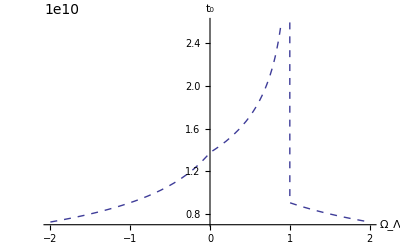

```mathematica
H0 = 2.3*^-18*3.16*^7 (*Hubble constatnt in inverese years*)

(*Plots of t vs Omega================================================*)
func1 = 1/(H0*Sqrt[Omeg])ArcSinh[Sqrt[Omeg/(1-Omeg)]];
func2 = 1/(H0*Sqrt[Abs[Omeg]])ArcSinh[Sqrt[Abs[Omeg]/(1+Abs[Omeg])]];

Plot[{Piecewise[{{func1,Omeg<1&&Omeg>0},{func2,Omeg>1},{func2,Omeg<0}}]},{Omeg,-2,2},AxesLabel->{Subscript[Ω,Λ],Subscript[t,0]},PlotStyle->{Dashed,Thick}]
```

```mathematica
(*a(t) For Big Bang=========================================================*)
```

```mathematica
func3 = Sqrt[(1-Omeg)/Omeg]Sinh[H0*Sqrt[Omeg]t];
func4 = Sqrt[(1+Abs[Omeg])/Abs[Omeg]]Sin[H0*Sqrt[Abs[Omeg]]t];
Plot3D[func3,{Omeg,0,1},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ],t,a}]
```

-Graphics3D-

```mathematica
Plot3D[func4,{Omeg,0,-2},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ],t,a}]
```

-Graphics3D-

```mathematica
Plot3D[func4,{Omeg,1,2},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ],t,a}]
```

-Graphics3D-

```mathematica
(*No Big Bang Soluton=============================================================*)
t0 = 1;H02=1;
OmegPlus  = (Sqrt[Omeg]-1)/(2Sqrt[Omeg]);
OmegMinus  = (Sqrt[Omeg]+1)/(2Sqrt[Omeg]);OmegPlus2  = (I*Sqrt[Abs[Omeg]]-1)/(2I*Sqrt[Abs[Omeg]]); OmegMinus2  = (I*Sqrt[Abs[Omeg]]+1)/(2I*Sqrt[Abs[Omeg]]);

func5 = OmegPlus*Exp[H02*Sqrt[Omeg]*(t-t0)]+OmegMinus*Exp[-H02*Sqrt[Omeg]*(t-t0)];
func6 = OmegPlus2*Exp[I*H02*Sqrt[Abs[Omeg]]*(t-t0)]+OmegMinus2*Exp[-I*H02*Sqrt[Abs[Omeg]]*(t-t0)];
```

```mathematica
Plot3D[func5,{Omeg,0,2},{t,0,3},AxesLabel->{Subscript[Ω,Λ],t,a}]
```

-Graphics3D-

```mathematica
Plot3D[func6,{Omeg,0,-2},{t,0,10},AxesLabel->{Subscript[Ω,Λ],t,a}]
```

-Graphics3D-

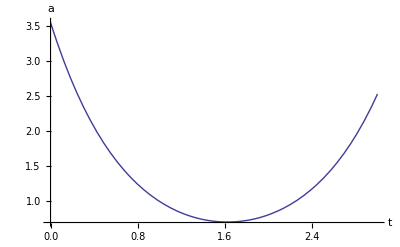

```mathematica
Plot[func5/.Omeg->2,{t,0,3},AxesLabel->{t,a}]
```

```mathematica
(*OmegaLambda vs time==========================================*)
(*OmegaA1 = Omeg*H0*func3^2/D[func3,t];
OmegaA2 = Omeg*H0*func4^2/D[func4,t];*)
OmegaA1 =( Tanh[Sqrt[Omeg]*H0*t])^2;
OmegaA2 =( Tan[Sqrt[Abs[Omeg]]*H0*t])^2;


Plot3D[OmegaA1,{Omeg,0,1},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ0],t,Ω}]
```

-Graphics3D-

```mathematica
Plot3D[OmegaA2,{Omeg,1,2},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ0],t,Ω}]
```

-Graphics3D-

```mathematica
Plot3D[OmegaA2,{Omeg,0,-2},{t,0,10/H0},AxesLabel->{Subscript[Ω,Λ0],t,Ω}]
```

-Graphics3D-

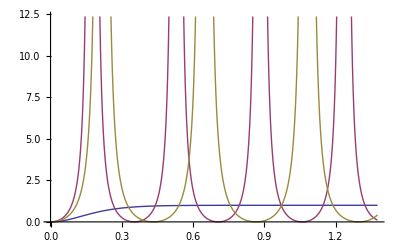

```mathematica
Plot[{OmegaA1/.Omeg->.5,OmegaA2/.Omeg->1.5,OmegaA2/.Omeg->-1},{t,0,10/H0}]
```